## Boltzmann equation

### preliminaries

```mathematica
xifs[t_]:=(1+xi0)(t/t0)^2-1
```

```mathematica
R[z_]:=1/2(1/(1+z)+ArcTan[Sqrt[z]]/Sqrt[z])
```

```mathematica
Tlast[t_]:=(elast[t]/gamma)^(1/4)
```

```mathematica
tppint[t_]:=NIntegrate[Tlast[tpp]/c1,{tpp,t0,t}]
```

```mathematica
Dnew[t2_,t1_]:=Exp[-Itppint[t2]+Itppint[t1]]
```

```mathematica
enew[t_]:=Dnew[t,t0]R[xifs[t]]+NIntegrate[Dnew[t,tp]elast[tp]R[(t/tp)^2-1]/c1 Tlast[tp],{tp,t0,t},PrecisionGoal->5]
```

### numerics

```mathematica
t0=0.1;xi0=5.0;c1=0.4;gamma=6/Pi^2;stop=200 t0;step=0.1t0;
```

```mathematica
elast[t_]=0.1/t; It=0;
```

```mathematica
Do[ttab=Table[{x^4,tppint[x^4]},{x,t0^(1/4),stop^(1/4),step}];Itppint[t_]=Interpolation[ttab][t];tnew=Table[{x^4,enew[x^4]},{x,t0^(1/4),stop^(1/4),step}];elast[t_]=Interpolation[tnew][t];
Print["Iteration ",It," done!"];It=It+1;mye[It]=elast[t];,{i,1,3}];
```

30

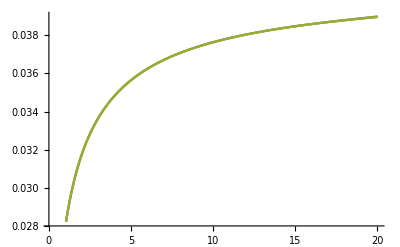

```mathematica
Print[It];Plot[{mye[It-2]t^(4/3),mye[It-1]t^(4/3),mye[It]t^(4/3)},{t,t0,stop}]
```

```mathematica
ffx0[t_]=(t D[mye[It],t]/mye[It])/4+1
```

1+(t InterpolatingFunction[{{0.1, 19.9093}}, <>][t])/(4 InterpolatingFunction[{{0.1, 19.9093}}, <>][t])

```mathematica
fftab=Table[{t Tlast[t],ffx0[t]},{t,t0,stop 0.7,step}]
```

{{0.0865125,0.725071},{0.0927075,0.726708},{0.0987674,0.728611},{0.104704,0.730023},{0.110528,0.73106},{0.116248,0.731821},{0.121871,0.732053},{0.127404,0.732772},{0.132853,0.73304},{0.138224,0.733201},{0.143521,0.733273},{0.148749,0.733275},{0.153911,0.73323},{0.15901,0.733162},{0.164051,0.733266},{0.169034,0.733092},{0.173965,0.732906},{0.178844,0.73292},{0.183674,0.732681},{0.188457,0.732439},{0.193195,0.732386},{0.19789,0.732107},{0.202543,0.732023},{0.207156,0.731736},{0.21173,0.731446},{0.216267,0.731329},{0.220768,0.731022},{0.225234,0.730895},{0.229666,0.730581},{0.234066,0.730443},{0.238434,0.730125},{0.242771,0.729978},{0.247078,0.72966},{0.251357,0.729506},{0.255607,0.729189},{0.259829,0.729029},{0.264026,0.728717},{0.268195,0.728548},{0.27234,0.728249},{0.27646,0.728067},{0.280556,0.7279},{0.284629,0.727589},{0.288678,0.727421},{0.292705,0.727119},{0.29671,0.726942},{0.300694,0.726772},{0.304656,0.726469},{0.308599,0.7263},{0.312521,0.72601},{0.316423,0.725829},{0.320306,0.725662},{0.324171,0.72537},{0.328017,0.725198},{0.331844,0.72503},{0.335654,0.724742},{0.339447,0.724573},{0.343222,0.724406},{0.346981,0.724123},{0.350723,0.723958},{0.354449,0.723792},{0.358159,0.723515},{0.361853,0.723351},{0.365532,0.723188},{0.369196,0.722917},{0.372844,0.722755},{0.376479,0.722595},{0.380099,0.722331},{0.383704,0.722168},{0.387296,0.722012},{0.390874,0.721757},{0.394439,0.721593},{0.39799,0.721439},{0.401528,0.721282},{0.405054,0.721029},{0.408566,0.720875},{0.412066,0.720724},{0.415554,0.720479},{0.419029,0.720322},{0.422493,0.720174},{0.425944,0.720024},{0.429384,0.719783},{0.432813,0.719634},{0.43623,0.719489},{0.439636,0.71934},{0.443031,0.719106},{0.446414,0.718962},{0.449788,0.71882},{0.45315,0.718595},{0.456502,0.718445},{0.459844,0.718305},{0.463175,0.718167},{0.466496,0.717946},{0.469807,0.717801},{0.473109,0.717664},{0.4764,0.717529},{0.479682,0.717389},{0.482955,0.717172},{0.486218,0.717038},{0.489471,0.716906},{0.492716,0.716771},{0.495951,0.716559},{0.499177,0.716427},{0.502395,0.716298},{0.505604,0.716168},{0.508804,0.715961},{0.511995,0.71583},{0.515178,0.715704},{0.518352,0.715578},{0.521518,0.715449},{0.524676,0.715248},{0.527825,0.715123},{0.530967,0.715001},{0.5341,0.714878},{0.537226,0.714682},{0.540344,0.714557},{0.543454,0.714437},{0.546556,0.714318},{0.549651,0.714197},{0.552738,0.714006},{0.555817,0.713886},{0.55889,0.71377},{0.561955,0.713654},{0.565012,0.713536},{0.568063,0.71335},{0.571106,0.713234},{0.574142,0.713121},{0.577172,0.713008},{0.580194,0.712893},{0.58321,0.712712},{0.586218,0.712599},{0.58922,0.712489},{0.592216,0.71238},{0.595205,0.712269},{0.598187,0.712093},{0.601162,0.711982},{0.604131,0.711875},{0.607094,0.711769},{0.610051,0.711662},{0.613001,0.711491},{0.615945,0.711382},{0.618882,0.711277},{0.621814,0.711174},{0.62474,0.711071},{0.627659,0.710965},{0.630573,0.710798},{0.63348,0.710695},{0.636382,0.710594},{0.639278,0.710494},{0.642168,0.710393},{0.645052,0.710232},{0.647931,0.710129},{0.650804,0.71003},{0.653671,0.709933},{0.656533,0.709836},{0.659389,0.709737},{0.66224,0.709579},{0.665085,0.709481},{0.667925,0.709385},{0.67076,0.709291},{0.673589,0.709197},{0.676413,0.7091},{0.679232,0.708947},{0.682045,0.708852},{0.684854,0.70876},{0.687657,0.708668},{0.690455,0.708577},{0.693248,0.708484},{0.696036,0.708335},{0.698819,0.708242},{0.701597,0.708152},{0.70437,0.708064},{0.707139,0.707975},{0.709902,0.707886},{0.712661,0.707741},{0.715415,0.707651},{0.718164,0.707563},{0.720908,0.707477},{0.723648,0.707391},{0.726383,0.707305},{0.729114,0.707165},{0.731839,0.707076},{0.734561,0.706991},{0.737277,0.706907},{0.73999,0.706824},{0.742698,0.706741},{0.745401,0.706656},{0.7481,0.70652},{0.750794,0.706435},{0.753485,0.706353},{0.75617,0.706272},{0.758852,0.706192},{0.761529,0.706111},{0.764203,0.706029},{0.766871,0.705896},{0.769536,0.705815},{0.772196,0.705736},{0.774853,0.705658},{0.777505,0.70558},{0.780153,0.705502},{0.782797,0.705374},{0.785437,0.705293},{0.788073,0.705215},{0.790705,0.705138},{0.793333,0.705063},{0.795957,0.704988},{0.798577,0.704912},{0.801194,0.704834},{0.803806,0.704709},{0.806414,0.704634},{0.809019,0.70456},{0.81162,0.704486},{0.814217,0.704414},{0.81681,0.704341},{0.8194,0.704266},{0.821986,0.704144},{0.824568,0.70407},{0.827146,0.703998},{0.829721,0.703928},{0.832292,0.703857},{0.83486,0.703787},{0.837424,0.703715},{0.839984,0.703597},{0.842541,0.703525},{0.845094,0.703454},{0.847644,0.703385},{0.85019,0.703317},{0.852733,0.703249},{0.855272,0.703181},{0.857808,0.703111},{0.86034,0.702996},{0.862869,0.702927},{0.865395,0.70286},{0.867917,0.702793},{0.870436,0.702728},{0.872951,0.702662},{0.875464,0.702595},{0.877973,0.702484},{0.880478,0.702416},{0.88298,0.70235},{0.885479,0.702285},{0.887975,0.702221},{0.890468,0.702157},{0.892957,0.702094},{0.895444,0.702029},{0.897927,0.701921},{0.900406,0.701855},{0.902883,0.701791},{0.905357,0.701729},{0.907827,0.701667},{0.910295,0.701605},{0.912759,0.701544},{0.91522,0.701482},{0.917679,0.701419},{0.920134,0.701313},{0.922586,0.701251},{0.925035,0.701191},{0.927481,0.701131},{0.929924,0.701071},{0.932365,0.701012},{0.934802,0.700952},{0.937236,0.700892},{0.939668,0.700789},{0.942096,0.700729},{0.944522,0.700669},{0.946945,0.700611},{0.949365,0.700554},{0.951782,0.700497},{0.954196,0.700439},{0.956607,0.700381},{0.959016,0.700282},{0.961422,0.700223},{0.963825,0.700165},{0.966225,0.700108},{0.968622,0.700052},{0.971017,0.699997},{0.973409,0.699942},{0.975798,0.699886},{0.978185,0.69983},{0.980569,0.699733},{0.98295,0.699676},{0.985328,0.699621},{0.987704,0.699566},{0.990077,0.699513},{0.992448,0.699459},{0.994815,0.699406},{0.997181,0.699352},{0.999543,0.699298},{1.0019,0.699204},{1.00426,0.699149},{1.00662,0.699095},{1.00897,0.699043},{1.01132,0.698991},{1.01367,0.698939},{1.01601,0.698888},{1.01835,0.698836},{1.02069,0.698784},{1.02303,0.698692},{1.02536,0.698639},{1.0277,0.698588},{1.03003,0.698537},{1.03235,0.698486},{1.03468,0.698437},{1.037,0.698387},{1.03932,0.698337},{1.04164,0.698287},{1.04395,0.698236},{1.04627,0.698147},{1.04858,0.698096},{1.05088,0.698047},{1.05319,0.697998},{1.05549,0.69795},{1.05779,0.697902},{1.06009,0.697854},{1.06239,0.697806},{1.06468,0.697757},{1.06697,0.697671},{1.06926,0.697621},{1.07155,0.697573},{1.07384,0.697526},{1.07612,0.697479},{1.0784,0.697432},{1.08068,0.697386},{1.08295,0.69734},{1.08523,0.697293},{1.0875,0.697246},{1.08977,0.697162},{1.09203,0.697115},{1.0943,0.697068},{1.09656,0.697023},{1.09882,0.696978},{1.10108,0.696933},{1.10333,0.696888},{1.10559,0.696844},{1.10784,0.696799},{1.11009,0.696753},{1.11234,0.696671},{1.11458,0.696626},{1.11682,0.696581},{1.11907,0.696537},{1.1213,0.696493},{1.12354,0.69645},{1.12578,0.696407},{1.12801,0.696364},{1.13024,0.696321},{1.13247,0.696277},{1.13469,0.696198},{1.13692,0.696153},{1.13914,0.69611},{1.14136,0.696067},{1.14358,0.696025},{1.14579,0.695984},{1.14801,0.695942},{1.15022,0.695901},{1.15243,0.695859},{1.15464,0.695817},{1.15685,0.695774},{1.15905,0.695697},{1.16125,0.695655},{1.16345,0.695614},{1.16565,0.695573},{1.16785,0.695532},{1.17004,0.695492},{1.17223,0.695452},{1.17442,0.695412},{1.17661,0.695372},{1.1788,0.695331},{1.18098,0.695257},{1.18317,0.695215},{1.18535,0.695175},{1.18753,0.695135},{1.1897,0.695096},{1.19188,0.695057},{1.19405,0.695018},{1.19622,0.69498},{1.19839,0.694941},{1.20056,0.694902},{1.20273,0.694863},{1.20489,0.69479},{1.20705,0.694751},{1.20921,0.694712},{1.21137,0.694673},{1.21353,0.694636},{1.21569,0.694598},{1.21784,0.694561},{1.21999,0.694524},{1.22214,0.694487},{1.22429,0.694449},{1.22643,0.694411},{1.22858,0.694341},{1.23072,0.694302},{1.23286,0.694265},{1.235,0.694228},{1.23714,0.694191},{1.23927,0.694155},{1.24141,0.694119},{1.24354,0.694083},{1.24567,0.694047},{1.2478,0.694011},{1.24992,0.693975},{1.25205,0.693938},{1.25417,0.693869},{1.25629,0.693833},{1.25841,0.693797},{1.26053,0.693761},{1.26265,0.693726},{1.26476,0.693692},{1.26688,0.693657},{1.26899,0.693623},{1.2711,0.693588},{1.27321,0.693553},{1.27531,0.693518},{1.27742,0.693451},{1.27952,0.693416},{1.28162,0.693381},{1.28372,0.693346},{1.28582,0.693312},{1.28792,0.693279},{1.29001,0.693245},{1.29211,0.693212},{1.2942,0.693179},{1.29629,0.693145},{1.29838,0.693112},{1.30047,0.693078},{1.30255,0.693013},{1.30464,0.692979},{1.30672,0.692945},{1.3088,0.692912},{1.31088,0.692879},{1.31296,0.692847},{1.31503,0.692814},{1.31711,0.692782},{1.31918,0.69275},{1.32125,0.692718},{1.32332,0.692686},{1.32539,0.692653},{1.32746,0.69259},{1.32952,0.692557},{1.33159,0.692524},{1.33365,0.692492},{1.33571,0.692461},{1.33777,0.69243},{1.33982,0.692399},{1.34188,0.692368},{1.34394,0.692337},{1.34599,0.692306},{1.34804,0.692275},{1.35009,0.692244},{1.35214,0.692212},{1.35419,0.69215},{1.35623,0.692119},{1.35828,0.692088},{1.36032,0.692057},{1.36236,0.692027},{1.3644,0.691997},{1.36644,0.691967},{1.36848,0.691937},{1.37051,0.691907},{1.37255,0.691878},{1.37458,0.691848},{1.37661,0.691817},{1.37864,0.691758},{1.38067,0.691727},{1.3827,0.691697},{1.38472,0.691667},{1.38675,0.691637},{1.38877,0.691608},{1.39079,0.691579},{1.39281,0.691551},{1.39483,0.691522},{1.39685,0.691494},{1.39886,0.691465},{1.40088,0.691436},{1.40289,0.691407},{1.4049,0.691348},{1.40691,0.691319},{1.40892,0.69129},{1.41093,0.691261},{1.41293,0.691233},{1.41494,0.691205},{1.41694,0.691177},{1.41894,0.691149},{1.42094,0.691122},{1.42294,0.691094},{1.42494,0.691067},{1.42694,0.691039},{1.42893,0.691011},{1.43093,0.690954},{1.43292,0.690925},{1.43491,0.690897},{1.4369,0.69087},{1.43889,0.690842},{1.44088,0.690815},{1.44287,0.690788},{1.44485,0.690762},{1.44683,0.690735},{1.44882,0.690709},{1.4508,0.690682},{1.45278,0.690655},{1.45475,0.690628},{1.45673,0.690601},{1.45871,0.690546},{1.46068,0.690519},{1.46266,0.690492},{1.46463,0.690465},{1.4666,0.690439},{1.46857,0.690413},{1.47054,0.690387},{1.4725,0.690362},{1.47447,0.690336},{1.47643,0.690311},{1.4784,0.690285},{1.48036,0.690259},{1.48232,0.690233},{1.48428,0.690207},{1.48624,0.690153},{1.48819,0.690127},{1.49015,0.690101},{1.4921,0.690076},{1.49406,0.690051},{1.49601,0.690026},{1.49796,0.690001},{1.49991,0.689976},{1.50186,0.689952},{1.5038,0.689927},{1.50575,0.689902},{1.50769,0.689877},{1.50964,0.689852},{1.51158,0.689827},{1.51352,0.689774},{1.51546,0.689749},{1.5174,0.689724},{1.51934,0.6897},{1.52127,0.689676},{1.52321,0.689652},{1.52514,0.689628},{1.52708,0.689604},{1.52901,0.68958},{1.53094,0.689557},{1.53287,0.689533},{1.5348,0.689509},{1.53672,0.689485},{1.53865,0.689461},{1.54057,0.689409},{1.5425,0.689385},{1.54442,0.689361},{1.54634,0.689337},{1.54826,0.689314},{1.55018,0.689291},{1.5521,0.689268},{1.55401,0.689245},{1.55593,0.689222},{1.55784,0.689199},{1.55976,0.689176},{1.56167,0.689153},{1.56358,0.68913},{1.56549,0.689107},{1.5674,0.689057},{1.56931,0.689034},{1.57121,0.68901},{1.57312,0.688987},{1.57502,0.688965},{1.57693,0.688942},{1.57883,0.68892},{1.58073,0.688898},{1.58263,0.688876},{1.58453,0.688854},{1.58643,0.688832},{1.58832,0.68881},{1.59022,0.688788},{1.59211,0.688765},{1.59401,0.688743},{1.5959,0.688694},{1.59779,0.688672},{1.59968,0.688649},{1.60157,0.688627},{1.60346,0.688605},{1.60534,0.688584},{1.60723,0.688562},{1.60911,0.688541},{1.611,0.68852},{1.61288,0.688499},{1.61476,0.688477},{1.61664,0.688456},{1.61852,0.688435},{1.6204,0.688413},{1.62228,0.688392},{1.62415,0.688345},{1.62603,0.688323},{1.6279,0.688301},{1.62978,0.68828},{1.63165,0.688259},{1.63352,0.688238},{1.63539,0.688217},{1.63726,0.688197},{1.63913,0.688176},{1.64099,0.688156},{1.64286,0.688136},{1.64473,0.688115},{1.64659,0.688095},{1.64845,0.688074},{1.65031,0.688053},{1.65218,0.688032},{1.65404,0.687986},{1.65589,0.687965},{1.65775,0.687945},{1.65961,0.687924},{1.66147,0.687904},{1.66332,0.687884},{1.66517,0.687864},{1.66703,0.687845},{1.66888,0.687825},{1.67073,0.687805},{1.67258,0.687786},{1.67443,0.687766},{1.67628,0.687746},{1.67812,0.687726},{1.67997,0.687706},{1.68181,0.687661},{1.68366,0.687641},{1.6855,0.687621},{1.68734,0.687601},{1.68919,0.687582},{1.69103,0.687562},{1.69286,0.687543},{1.6947,0.687524},{1.69654,0.687505},{1.69838,0.687486},{1.70021,0.687467},{1.70205,0.687448},{1.70388,0.687429},{1.70571,0.68741},{1.70754,0.687391},{1.70937,0.687372},{1.7112,0.687328},{1.71303,0.687308},{1.71486,0.687289},{1.71669,0.68727},{1.71851,0.687251},{1.72034,0.687233},{1.72216,0.687214},{1.72399,0.687196},{1.72581,0.687177},{1.72763,0.687159},{1.72945,0.687141},{1.73127,0.687123},{1.73309,0.687104},{1.7349,0.687086},{1.73672,0.687068},{1.73854,0.687049},{1.74035,0.68703},{1.74217,0.686988},{1.74398,0.686969},{1.74579,0.686951},{1.7476,0.686932},{1.74941,0.686914},{1.75122,0.686896},{1.75303,0.686879},{1.75484,0.686861},{1.75664,0.686843},{1.75845,0.686826},{1.76025,0.686808},{1.76206,0.686791},{1.76386,0.686773},{1.76566,0.686755},{1.76747,0.686738},{1.76927,0.68672},{1.77107,0.686678},{1.77286,0.68666},{1.77466,0.686642},{1.77646,0.686624},{1.77825,0.686607},{1.78005,0.68659},{1.78184,0.686572},{1.78364,0.686555},{1.78543,0.686538},{1.78722,0.686521},{1.78901,0.686505},{1.7908,0.686488},{1.79259,0.686471},{1.79438,0.686454},{1.79617,0.686437},{1.79795,0.68642},{1.79974,0.686402},{1.80152,0.686362},{1.80331,0.686344},{1.80509,0.686327},{1.80687,0.68631},{1.80865,0.686293},{1.81043,0.686276},{1.81221,0.68626},{1.81399,0.686243},{1.81577,0.686227},{1.81755,0.686211},{1.81932,0.686195},{1.8211,0.686178},{1.82287,0.686162},{1.82465,0.686146},{1.82642,0.686129},{1.82819,0.686113},{1.82996,0.686096},{1.83173,0.686057},{1.8335,0.68604},{1.83527,0.686023},{1.83704,0.686007},{1.83881,0.68599},{1.84057,0.685974},{1.84234,0.685958},{1.8441,0.685942},{1.84587,0.685927},{1.84763,0.685911},{1.84939,0.685895},{1.85115,0.68588},{1.85291,0.685864},{1.85467,0.685848},{1.85643,0.685832},{1.85819,0.685817},{1.85995,0.685801},{1.86171,0.685785},{1.86346,0.685746},{1.86522,0.68573},{1.86697,0.685714},{1.86872,0.685698},{1.87048,0.685682},{1.87223,0.685667},{1.87398,0.685652},{1.87573,0.685636},{1.87748,0.685621},{1.87923,0.685606},{1.88097,0.685591},{1.88272,0.685576},{1.88447,0.685561},{1.88621,0.685546},{1.88796,0.68553},{1.8897,0.685515},{1.89144,0.6855},{1.89319,0.685484},{1.89493,0.685447},{1.89667,0.685431},{1.89841,0.685416},{1.90015,0.6854},{1.90189,0.685385},{1.90362,0.68537},{1.90536,0.685356},{1.9071,0.685341},{1.90883,0.685326},{1.91057,0.685312},{1.9123,0.685297},{1.91403,0.685283},{1.91577,0.685268},{1.9175,0.685254},{1.91923,0.685239},{1.92096,0.685224},{1.92269,0.68521},{1.92442,0.685195},{1.92614,0.685158},{1.92787,0.685143},{1.9296,0.685128},{1.93132,0.685113},{1.93305,0.685099},{1.93477,0.685084},{1.9365,0.68507},{1.93822,0.685056},{1.93994,0.685042},{1.94166,0.685028},{1.94338,0.685014},{1.9451,0.685},{1.94682,0.684986},{1.94854,0.684972},{1.95026,0.684958},{1.95197,0.684944},{1.95369,0.684929},{1.9554,0.684915},{1.95712,0.684901},{1.95883,0.684865},{1.96054,0.68485},{1.96226,0.684836},{1.96397,0.684822},{1.96568,0.684808},{1.96739,0.684794},{1.9691,0.684781},{1.97081,0.684767},{1.97251,0.684753},{1.97422,0.68474},{1.97593,0.684726},{1.97763,0.684713},{1.97934,0.684699},{1.98104,0.684686},{1.98275,0.684672},{1.98445,0.684659},{1.98615,0.684645},{1.98785,0.684631},{1.98955,0.684617},{1.99126,0.684582},{1.99295,0.684568},{1.99465,0.684555},{1.99635,0.684541},{1.99805,0.684528},{1.99974,0.684514},{2.00144,0.684501},{2.00314,0.684488},{2.00483,0.684475},{2.00652,0.684462},{2.00822,0.684449},{2.00991,0.684436},{2.0116,0.684423},{2.01329,0.68441},{2.01498,0.684397},{2.01667,0.684384},{2.01836,0.684371},{2.02005,0.684357},{2.02174,0.684344},{2.02342,0.68431},{2.02511,0.684296},{2.0268,0.684283},{2.02848,0.68427},{2.03017,0.684257},{2.03185,0.684244},{2.03353,0.684231},{2.03521,0.684219},{2.03689,0.684206},{2.03858,0.684193},{2.04026,0.684181},{2.04194,0.684168},{2.04361,0.684156},{2.04529,0.684143},{2.04697,0.684131},{2.04865,0.684118},{2.05032,0.684106},{2.052,0.684093},{2.05367,0.68408},{2.05535,0.684047},{2.05702,0.684034},{2.05869,0.684021},{2.06037,0.684008},{2.06204,0.683996},{2.06371,0.683983},{2.06538,0.683971},{2.06705,0.683958},{2.06872,0.683946},{2.07038,0.683934},{2.07205,0.683922},{2.07372,0.68391},{2.07538,0.683898},{2.07705,0.683886},{2.07872,0.683874},{2.08038,0.683862},{2.08204,0.68385},{2.08371,0.683837},{2.08537,0.683825},{2.08703,0.683813},{2.08869,0.68378},{2.09035,0.683768},{2.09201,0.683755},{2.09367,0.683743},{2.09533,0.683731},{2.09699,0.683719},{2.09864,0.683707},{2.1003,0.683695},{2.10196,0.683683},{2.10361,0.683672},{2.10527,0.68366},{2.10692,0.683648},{2.10857,0.683637},{2.11023,0.683625},{2.11188,0.683613},{2.11353,0.683602},{2.11518,0.68359},{2.11683,0.683578},{2.11848,0.683567},{2.12013,0.683555},{2.12178,0.683523},{2.12343,0.683511},{2.12507,0.683499},{2.12672,0.683487},{2.12837,0.683475},{2.13001,0.683464},{2.13166,0.683452},{2.1333,0.683441},{2.13494,0.683429},{2.13659,0.683418},{2.13823,0.683407},{2.13987,0.683396},{2.14151,0.683384},{2.14315,0.683373},{2.14479,0.683362},{2.14643,0.683351},{2.14807,0.68334},{2.14971,0.683328},{2.15134,0.683317},{2.15298,0.683305},{2.15462,0.683294},{2.15625,0.683263},{2.15789,0.683251},{2.15952,0.68324},{2.16116,0.683228},{2.16279,0.683217},{2.16442,0.683206},{2.16605,0.683195},{2.16768,0.683184},{2.16931,0.683173},{2.17094,0.683162},{2.17257,0.683151},{2.1742,0.68314},{2.17583,0.68313},{2.17746,0.683119},{2.17909,0.683108},{2.18071,0.683097},{2.18234,0.683086},{2.18396,0.683075},{2.18559,0.683065},{2.18721,0.683053},{2.18884,0.683042},{2.19046,0.683012},{2.19208,0.683001},{2.1937,0.68299},{2.19532,0.682979},{2.19695,0.682968},{2.19857,0.682957},{2.20019,0.682946},{2.2018,0.682936},{2.20342,0.682925},{2.20504,0.682915},{2.20666,0.682904},{2.20827,0.682894},{2.20989,0.682884},{2.21151,0.682873},{2.21312,0.682863},{2.21473,0.682852},{2.21635,0.682842},{2.21796,0.682831},{2.21957,0.682821},{2.22119,0.68281},{2.2228,0.6828},{2.22441,0.68277},{2.22602,0.682759},{2.22763,0.682748},{2.22924,0.682738},{2.23085,0.682727},{2.23245,0.682717},{2.23406,0.682707},{2.23567,0.682696},{2.23727,0.682686},{2.23888,0.682676},{2.24049,0.682666},{2.24209,0.682656},{2.24369,0.682646},{2.2453,0.682636},{2.2469,0.682626},{2.2485,0.682616},{2.25011,0.682606},{2.25171,0.682596},{2.25331,0.682585},{2.25491,0.682575},{2.25651,0.682565},{2.25811,0.682555},{2.2597,0.682526},{2.2613,0.682515},{2.2629,0.682505},{2.2645,0.682495},{2.26609,0.682485},{2.26769,0.682475},{2.26928,0.682465},{2.27088,0.682455},{2.27247,0.682445},{2.27407,0.682435},{2.27566,0.682426},{2.27725,0.682416},{2.27884,0.682406},{2.28044,0.682397},{2.28203,0.682387},{2.28362,0.682377},{2.28521,0.682368},{2.2868,0.682358},{2.28839,0.682348},{2.28997,0.682338},{2.29156,0.682328},{2.29315,0.682318},{2.29473,0.68229},{2.29632,0.68228},{2.29791,0.68227},{2.29949,0.68226},{2.30108,0.68225},{2.30266,0.682241},{2.30424,0.682231},{2.30583,0.682222},{2.30741,0.682212},{2.30899,0.682203},{2.31057,0.682193},{2.31215,0.682184},{2.31373,0.682175},{2.31531,0.682165},{2.31689,0.682156},{2.31847,0.682147},{2.32005,0.682137},{2.32163,0.682128},{2.3232,0.682119},{2.32478,0.682109},{2.32635,0.6821},{2.32793,0.68209},{2.32951,0.68208},{2.33108,0.682053},{2.33265,0.682043},{2.33423,0.682033},{2.3358,0.682024},{2.33737,0.682015},{2.33894,0.682005},{2.34052,0.681996},{2.34209,0.681987},{2.34366,0.681978},{2.34523,0.681969},{2.3468,0.68196},{2.34836,0.681951},{2.34993,0.681942},{2.3515,0.681933},{2.35307,0.681924},{2.35463,0.681915},{2.3562,0.681906},{2.35777,0.681897},{2.35933,0.681888},{2.3609,0.681879},{2.36246,0.681869},{2.36402,0.68186},{2.36559,0.681851},{2.36715,0.681824},{2.36871,0.681814},{2.37027,0.681805},{2.37184,0.681796},{2.3734,0.681787},{2.37496,0.681778},{2.37652,0.681769},{2.37808,0.68176},{2.37963,0.681752},{2.38119,0.681743},{2.38275,0.681734},{2.38431,0.681726},{2.38586,0.681717},{2.38742,0.681708},{2.38898,0.6817},{2.39053,0.681691},{2.39209,0.681682},{2.39364,0.681674},{2.39519,0.681665},{2.39675,0.681656},{2.3983,0.681647},{2.39985,0.681638},{2.4014,0.681629},{2.40295,0.681603},{2.40451,0.681594},{2.40606,0.681585},{2.40761,0.681576},{2.40915,0.681567},{2.4107,0.681559},{2.41225,0.68155},{2.4138,0.681541},{2.41535,0.681533},{2.41689,0.681525},{2.41844,0.681516},{2.41999,0.681508},{2.42153,0.681499},{2.42308,0.681491},{2.42462,0.681483},{2.42617,0.681474},{2.42771,0.681466},{2.42925,0.681458},{2.43079,0.681449},{2.43234,0.681441},{2.43388,0.681432},{2.43542,0.681424},{2.43696,0.681415},{2.4385,0.681389},{2.44004,0.68138},{2.44158,0.681372},{2.44312,0.681363},{2.44466,0.681355},{2.44619,0.681346},{2.44773,0.681338},{2.44927,0.68133},{2.4508,0.681322},{2.45234,0.681313},{2.45388,0.681305},{2.45541,0.681297},{2.45695,0.681289},{2.45848,0.681281},{2.46001,0.681273},{2.46155,0.681265},{2.46308,0.681257},{2.46461,0.681249},{2.46614,0.681241},{2.46767,0.681233},{2.4692,0.681224},{2.47073,0.681216},{2.47226,0.681208},{2.47379,0.6812},{2.47532,0.681174},{2.47685,0.681166},{2.47838,0.681157},{2.47991,0.681149},{2.48143,0.681141},{2.48296,0.681133},{2.48449,0.681125},{2.48601,0.681117},{2.48754,0.681109},{2.48906,0.681101},{2.49059,0.681093},{2.49211,0.681085},{2.49363,0.681078},{2.49516,0.68107},{2.49668,0.681062},{2.4982,0.681054},{2.49972,0.681047},{2.50124,0.681039},{2.50277,0.681031},{2.50429,0.681023},{2.50581,0.681015},{2.50732,0.681007},{2.50884,0.680999},{2.51036,0.680991},{2.51188,0.680983},{2.5134,0.680958},{2.51491,0.68095},{2.51643,0.680942},{2.51795,0.680934},{2.51946,0.680927},{2.52098,0.680919},{2.52249,0.680911},{2.52401,0.680903},{2.52552,0.680896},{2.52704,0.680888},{2.52855,0.680881},{2.53006,0.680873},{2.53157,0.680866},{2.53308,0.680858},{2.5346,0.680851},{2.53611,0.680843},{2.53762,0.680836},{2.53913,0.680828},{2.54064,0.680821},{2.54215,0.680813},{2.54365,0.680806},{2.54516,0.680798},{2.54667,0.68079},{2.54818,0.680782},{2.54969,0.680775},{2.55119,0.68075},{2.5527,0.680742},{2.5542,0.680735},{2.55571,0.680727},{2.55721,0.68072},{2.55872,0.680712},{2.56022,0.680705},{2.56173,0.680697},{2.56323,0.68069},{2.56473,0.680683},{2.56623,0.680675},{2.56773,0.680668},{2.56924,0.680661},{2.57074,0.680654},{2.57224,0.680646},{2.57374,0.680639},{2.57524,0.680632},{2.57674,0.680625},{2.57823,0.680617},{2.57973,0.68061},{2.58123,0.680603},{2.58273,0.680595},{2.58423,0.680588},{2.58572,0.680581},{2.58722,0.680573},{2.58871,0.680549},{2.59021,0.680542},{2.5917,0.680534},{2.5932,0.680527},{2.59469,0.680519},{2.59619,0.680512},{2.59768,0.680505},{2.59917,0.680498},{2.60067,0.680491},{2.60216,0.680484},{2.60365,0.680477},{2.60514,0.68047},{2.60663,0.680463},{2.60812,0.680456},{2.60961,0.680449},{2.6111,0.680442},{2.61259,0.680435},{2.61408,0.680428},{2.61557,0.680421},{2.61705,0.680414},{2.61854,0.680407},{2.62003,0.6804},{2.62151,0.680393},{2.623,0.680385},{2.62449,0.680378},{2.62597,0.680355},{2.62746,0.680347},{2.62894,0.68034},{2.63043,0.680333},{2.63191,0.680326},{2.63339,0.680319},{2.63488,0.680312},{2.63636,0.680305},{2.63784,0.680298},{2.63932,0.680291},{2.6408,0.680284},{2.64228,0.680278},{2.64376,0.680271},{2.64524,0.680264},{2.64672,0.680257},{2.6482,0.680251},{2.64968,0.680244},{2.65116,0.680237},{2.65264,0.68023},{2.65412,0.680224},{2.65559,0.680217},{2.65707,0.68021},{2.65855,0.680203},{2.66002,0.680196},{2.6615,0.68019},{2.66297,0.680183},{2.66445,0.68016},{2.66592,0.680153},{2.6674,0.680146},{2.66887,0.680139},{2.67034,0.680132},{2.67182,0.680125},{2.67329,0.680118},{2.67476,0.680112},{2.67623,0.680105},{2.6777,0.680098},{2.67917,0.680092},{2.68064,0.680085},{2.68211,0.680079},{2.68358,0.680072},{2.68505,0.680066},{2.68652,0.680059},{2.68799,0.680053},{2.68946,0.680046},{2.69093,0.68004},{2.69239,0.680033},{2.69386,0.680027},{2.69533,0.68002},{2.69679,0.680014},{2.69826,0.680007},{2.69972,0.68},{2.70119,0.679994},{2.70265,0.679987},{2.70412,0.679964},{2.70558,0.679958},{2.70704,0.679951},{2.70851,0.679944},{2.70997,0.679938},{2.71143,0.679931},{2.71289,0.679925},{2.71436,0.679918},{2.71582,0.679912},{2.71728,0.679905},{2.71874,0.679899},{2.7202,0.679893},{2.72166,0.679886},{2.72312,0.67988},{2.72457,0.679874},{2.72603,0.679868},{2.72749,0.679861},{2.72895,0.679855},{2.73041,0.679849},{2.73186,0.679843},{2.73332,0.679836},{2.73478,0.67983},{2.73623,0.679824},{2.73769,0.679817},{2.73914,0.679811},{2.7406,0.679804},{2.74205,0.679798},{2.7435,0.679776},{2.74496,0.679769},{2.74641,0.679763},{2.74786,0.679756},{2.74932,0.67975},{2.75077,0.679744},{2.75222,0.679737},{2.75367,0.679731},{2.75512,0.679725},{2.75657,0.679719},{2.75802,0.679713},{2.75947,0.679707},{2.76092,0.679701},{2.76237,0.679694},{2.76382,0.679688},{2.76527,0.679682},{2.76671,0.679676},{2.76816,0.67967},{2.76961,0.679664},{2.77105,0.679658},{2.7725,0.679652},{2.77395,0.679646},{2.77539,0.67964},{2.77684,0.679634},{2.77828,0.679628},{2.77973,0.679621},{2.78117,0.679615},{2.78262,0.679593},{2.78406,0.679587},{2.7855,0.679581},{2.78694,0.679575},{2.78839,0.679569},{2.78983,0.679562},{2.79127,0.679556},{2.79271,0.67955},{2.79415,0.679544},{2.79559,0.679538},{2.79703,0.679532},{2.79847,0.679527},{2.79991,0.679521},{2.80135,0.679515},{2.80279,0.679509},{2.80423,0.679503},{2.80567,0.679497},{2.8071,0.679492},{2.80854,0.679486},{2.80998,0.67948},{2.81141,0.679474},{2.81285,0.679468},{2.81429,0.679462},{2.81572,0.679456},{2.81716,0.67945},{2.81859,0.679444},{2.82002,0.679438},{2.82146,0.679432},{2.82289,0.679411},{2.82433,0.679405},{2.82576,0.679399},{2.82719,0.679393},{2.82862,0.679387},{2.83006,0.679381},{2.83149,0.679375},{2.83292,0.67937},{2.83435,0.679364},{2.83578,0.679358},{2.83721,0.679352},{2.83864,0.679347},{2.84007,0.679341},{2.8415,0.679335},{2.84293,0.67933},{2.84435,0.679324},{2.84578,0.679319},{2.84721,0.679313},{2.84864,0.679307},{2.85006,0.679302},{2.85149,0.679296},{2.85292,0.67929},{2.85434,0.679285},{2.85577,0.679279},{2.85719,0.679273},{2.85862,0.679267},{2.86004,0.679262},{2.86147,0.679256},{2.86289,0.679235},{2.86431,0.679229},{2.86574,0.679223},{2.86716,0.679218},{2.86858,0.679212},{2.87,0.679206},{2.87142,0.679201},{2.87285,0.679195},{2.87427,0.679189},{2.87569,0.679184},{2.87711,0.679178},{2.87853,0.679173},{2.87995,0.679167},{2.88137,0.679162},{2.88279,0.679156},{2.8842,0.679151},{2.88562,0.679146},{2.88704,0.67914},{2.88846,0.679135},{2.88988,0.679129},{2.89129,0.679124},{2.89271,0.679118},{2.89412,0.679113},{2.89554,0.679108},{2.89696,0.679102},{2.89837,0.679096},{2.89979,0.679091},{2.9012,0.679085},{2.90261,0.67908},{2.90403,0.679059},{2.90544,0.679054},{2.90686,0.679048},{2.90827,0.679042},{2.90968,0.679037},{2.91109,0.679031}}

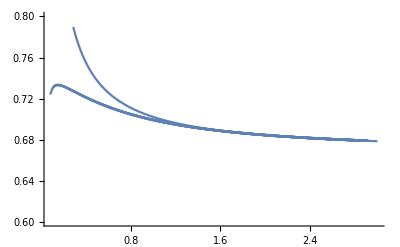

```mathematica
Show[ListPlot[fftab],Plot[2/3+4/9c1/5/x,{x,0.1,3}],PlotRange->{0.6,0.8}]
```

### Attractor

```mathematica
Clear[t0,xi0]
```

```mathematica
eprime[t0_,xi0_]=Evaluate[R'[xifs[t0]]xifs'[t0]];
```

```mathematica
e[t0_,xi0_]=R[xifs[t0]];
```

```mathematica
edprime[t0_,xi0_]=-R'[xifs[t0]]xifs'[t0]/c1 (e[t0,xi0]/gamma)^(1/4)+2 e[t0,xi0] (-2/3)/c1/t0 (e[t0,xi0]/gamma)^(1/4)+R''[xifs[t0]](xifs'[t0])^2+R'[xifs[t0]]xifs''[t0];
```

```mathematica
f[t0_,xi0_]=(eprime[t0,xi0] t0)/e[t0,xi0]/4+1;
```

```mathematica
fprime[t0_,xi0_]=(eprime[t0,xi0] e[t0,xi0]+t0 edprime[t0,xi0]e[t0,xi0]-t0 (eprime[t0,xi0])^2)/e[t0,xi0]^2;
```

```mathematica
myx[t0_]:=xi0/.FindRoot[fprime[t0,xi0]==0,{xi0,1,3}]
```

```mathematica
myx[0.1]
```

24.5311

### full attractor via numerics

```mathematica
t0=0.1;xi0=myx[t0];c1=0.4;gamma=6/Pi^2;stop=200 t0;step=0.1t0;
```

```mathematica
elast[t_]=0.1/t; It=0;
```

```mathematica
Do[ttab=Table[{x^4,tppint[x^4]},{x,t0^(1/4),stop^(1/4),step}];Itppint[t_]=Interpolation[ttab][t];tnew=Table[{x^4,enew[x^4]},{x,t0^(1/4),stop^(1/4),step}];elast[t_]=Interpolation[tnew][t];
Print["Iteration ",It," done!"];It=It+1;mye[It]=elast[t];,{i,1,30}];
```

Iteration 0 done!

Iteration 1 done!

Iteration 2 done!

Iteration 3 done!

Iteration 4 done!

Iteration 5 done!

Iteration 6 done!

Iteration 7 done!

Iteration 8 done!

Iteration 9 done!

Iteration 10 done!

Iteration 11 done!

Iteration 12 done!

Iteration 13 done!

Iteration 14 done!

Iteration 15 done!

Iteration 16 done!

Iteration 17 done!

Iteration 18 done!

Iteration 19 done!

Iteration 20 done!

Iteration 21 done!

Iteration 22 done!

Iteration 23 done!

Iteration 24 done!

Iteration 25 done!

Iteration 26 done!

Iteration 27 done!

Iteration 28 done!

Iteration 29 done!

30

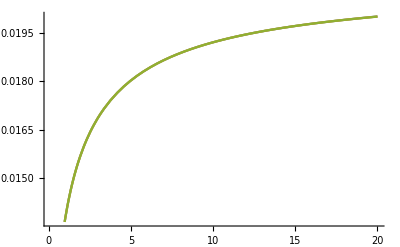

```mathematica
Print[It];Plot[{mye[It-2]t^(4/3),mye[It-1]t^(4/3),mye[It]t^(4/3)},{t,t0,stop}]
```

```mathematica
ffx0[t_]=(t D[mye[It],t]/mye[It])/4+1
```

1+(t InterpolatingFunction[{{0.1, 19.9093}}, <>][t])/(4 InterpolatingFunction[{{0.1, 19.9093}}, <>][t])

```mathematica
fftab=Table[{t Tlast[t],ffx0[t]},{t,t0,stop 0.7,step}]
```

{{0.0714169,0.742778},{0.0766524,0.742197},{0.0817659,0.742155},{0.0867693,0.742007},{0.0916728,0.741779},{0.0964846,0.741501},{0.101212,0.740923},{0.105862,0.74087},{0.110439,0.740531},{0.114949,0.740177},{0.119396,0.739812},{0.123783,0.73944},{0.128114,0.739072},{0.132392,0.738722},{0.13662,0.738563},{0.140801,0.738182},{0.144936,0.737814},{0.149028,0.737652},{0.153079,0.737277},{0.15709,0.736913},{0.161064,0.736741},{0.165001,0.736371},{0.168904,0.736194},{0.172772,0.735837},{0.176609,0.735486},{0.180414,0.735305},{0.184189,0.734952},{0.187935,0.734775},{0.191653,0.734426},{0.195344,0.73425},{0.199009,0.733907},{0.202648,0.733732},{0.206262,0.733395},{0.209852,0.733219},{0.213418,0.73289},{0.216962,0.732713},{0.220484,0.732394},{0.223983,0.732214},{0.227463,0.73191},{0.230921,0.731721},{0.23436,0.731549},{0.237778,0.731238},{0.241178,0.731068},{0.24456,0.730768},{0.247923,0.730591},{0.251269,0.730421},{0.254597,0.730124},{0.257908,0.729957},{0.261202,0.729673},{0.26448,0.729497},{0.267743,0.729333},{0.270989,0.72905},{0.274221,0.728883},{0.277437,0.72872},{0.280639,0.728442},{0.283826,0.72828},{0.286999,0.728119},{0.290158,0.727847},{0.293303,0.727688},{0.296436,0.72753},{0.299554,0.727264},{0.30266,0.727108},{0.305753,0.726953},{0.308834,0.726693},{0.311902,0.726539},{0.314959,0.726387},{0.318003,0.726134},{0.321036,0.72598},{0.324057,0.725832},{0.327067,0.725588},{0.330065,0.725432},{0.333053,0.725287},{0.33603,0.725139},{0.338996,0.724897},{0.341951,0.724752},{0.344896,0.724609},{0.347831,0.724375},{0.350756,0.724227},{0.353671,0.724087},{0.356577,0.723945},{0.359472,0.723715},{0.362358,0.723574},{0.365235,0.723437},{0.368102,0.723296},{0.37096,0.723072},{0.373809,0.722936},{0.376649,0.722803},{0.379481,0.722587},{0.382303,0.722446},{0.385118,0.722313},{0.387923,0.722182},{0.390721,0.721971},{0.393509,0.721834},{0.39629,0.721704},{0.399063,0.721576},{0.401828,0.721443},{0.404584,0.721236},{0.407333,0.721108},{0.410075,0.720984},{0.412809,0.720855},{0.415535,0.720652},{0.418253,0.720526},{0.420965,0.720404},{0.423669,0.72028},{0.426366,0.720082},{0.429055,0.719957},{0.431738,0.719837},{0.434414,0.719717},{0.437082,0.719594},{0.439744,0.719401},{0.442399,0.719282},{0.445048,0.719166},{0.44769,0.719048},{0.450325,0.71886},{0.452954,0.71874},{0.455576,0.718625},{0.458192,0.718512},{0.460802,0.718396},{0.463405,0.718212},{0.466002,0.718097},{0.468593,0.717985},{0.471178,0.717874},{0.473757,0.717761},{0.47633,0.717581},{0.478897,0.71747},{0.481458,0.717361},{0.484014,0.717253},{0.486564,0.717142},{0.489108,0.716967},{0.491646,0.716858},{0.494179,0.716753},{0.496706,0.716647},{0.499228,0.71654},{0.501744,0.716369},{0.504255,0.716262},{0.506761,0.716159},{0.509261,0.716056},{0.511756,0.715953},{0.514246,0.715787},{0.51673,0.715681},{0.51921,0.71558},{0.521684,0.71548},{0.524154,0.715379},{0.526618,0.715276},{0.529077,0.715115},{0.531532,0.715015},{0.533981,0.714917},{0.536426,0.71482},{0.538866,0.714721},{0.541301,0.714564},{0.543731,0.714464},{0.546157,0.714367},{0.548578,0.714272},{0.550995,0.714177},{0.553406,0.714081},{0.555814,0.713927},{0.558216,0.713831},{0.560615,0.713738},{0.563008,0.713645},{0.565398,0.713553},{0.567783,0.713459},{0.570163,0.713309},{0.57254,0.713216},{0.574912,0.713125},{0.577279,0.713035},{0.579643,0.712946},{0.582002,0.712854},{0.584357,0.712708},{0.586708,0.712617},{0.589055,0.712529},{0.591398,0.712442},{0.593737,0.712354},{0.596071,0.712266},{0.598402,0.712124},{0.600729,0.712035},{0.603051,0.711948},{0.60537,0.711863},{0.607685,0.711779},{0.609996,0.711693},{0.612304,0.711556},{0.614607,0.711468},{0.616906,0.711383},{0.619202,0.7113},{0.621494,0.711218},{0.623783,0.711135},{0.626067,0.711051},{0.628348,0.710917},{0.630626,0.710833},{0.632899,0.710751},{0.63517,0.710671},{0.637436,0.710591},{0.639699,0.71051},{0.641959,0.710428},{0.644214,0.710298},{0.646467,0.710217},{0.648716,0.710138},{0.650961,0.71006},{0.653203,0.709982},{0.655442,0.709904},{0.657677,0.709777},{0.659909,0.709697},{0.662138,0.709619},{0.664363,0.709542},{0.666585,0.709466},{0.668804,0.709391},{0.671019,0.709315},{0.673231,0.709237},{0.67544,0.709113},{0.677646,0.709037},{0.679848,0.708963},{0.682047,0.70889},{0.684243,0.708816},{0.686436,0.708743},{0.688626,0.708668},{0.690813,0.708547},{0.692997,0.708473},{0.695177,0.7084},{0.697355,0.708329},{0.699529,0.708258},{0.701701,0.708186},{0.703869,0.708114},{0.706035,0.707997},{0.708197,0.707924},{0.710357,0.707853},{0.712513,0.707783},{0.714667,0.707714},{0.716818,0.707645},{0.718966,0.707576},{0.721111,0.707505},{0.723253,0.70739},{0.725392,0.70732},{0.727529,0.707252},{0.729662,0.707185},{0.731793,0.707118},{0.733921,0.707051},{0.736047,0.706983},{0.738169,0.706873},{0.740289,0.706803},{0.742406,0.706736},{0.74452,0.70667},{0.746632,0.706604},{0.748741,0.70654},{0.750847,0.706475},{0.752951,0.706409},{0.755052,0.706301},{0.75715,0.706234},{0.759246,0.706169},{0.761339,0.706105},{0.763429,0.706041},{0.765517,0.705978},{0.767603,0.705915},{0.769686,0.705852},{0.771766,0.705787},{0.773844,0.705682},{0.775919,0.705618},{0.777991,0.705556},{0.780061,0.705495},{0.782129,0.705434},{0.784194,0.705373},{0.786257,0.705311},{0.788317,0.705249},{0.790375,0.705146},{0.792431,0.705084},{0.794484,0.705023},{0.796534,0.704963},{0.798582,0.704904},{0.800628,0.704845},{0.802672,0.704786},{0.804713,0.704726},{0.806751,0.704626},{0.808788,0.704565},{0.810822,0.704506},{0.812853,0.704447},{0.814883,0.70439},{0.81691,0.704332},{0.818935,0.704275},{0.820957,0.704218},{0.822978,0.704159},{0.824996,0.704062},{0.827011,0.704003},{0.829025,0.703946},{0.831036,0.703889},{0.833045,0.703834},{0.835052,0.703778},{0.837057,0.703723},{0.839059,0.703667},{0.84106,0.703611},{0.843058,0.703516},{0.845054,0.703459},{0.847047,0.703403},{0.849039,0.703349},{0.851029,0.703295},{0.853016,0.703241},{0.855001,0.703187},{0.856984,0.703133},{0.858966,0.703079},{0.860945,0.702987},{0.862921,0.702931},{0.864896,0.702877},{0.866869,0.702824},{0.86884,0.702772},{0.870808,0.70272},{0.872775,0.702668},{0.874739,0.702615},{0.876702,0.702563},{0.878663,0.70251},{0.880621,0.70242},{0.882578,0.702367},{0.884532,0.702315},{0.886485,0.702264},{0.888435,0.702214},{0.890384,0.702163},{0.892331,0.702113},{0.894275,0.702062},{0.896218,0.702011},{0.898159,0.701924},{0.900098,0.701872},{0.902035,0.701822},{0.90397,0.701772},{0.905903,0.701723},{0.907834,0.701674},{0.909764,0.701625},{0.911691,0.701576},{0.913617,0.701527},{0.91554,0.701477},{0.917462,0.701392},{0.919382,0.701343},{0.9213,0.701294},{0.923217,0.701246},{0.925131,0.701198},{0.927044,0.701151},{0.928955,0.701104},{0.930864,0.701056},{0.932771,0.701009},{0.934676,0.700961},{0.93658,0.700878},{0.938482,0.70083},{0.940382,0.700783},{0.94228,0.700736},{0.944177,0.70069},{0.946071,0.700644},{0.947964,0.700599},{0.949856,0.700553},{0.951745,0.700507},{0.953633,0.700461},{0.955519,0.70038},{0.957403,0.700333},{0.959286,0.700287},{0.961167,0.700242},{0.963046,0.700197},{0.964924,0.700153},{0.966799,0.700109},{0.968674,0.700065},{0.970546,0.70002},{0.972417,0.699976},{0.974286,0.699931},{0.976153,0.699852},{0.978019,0.699807},{0.979883,0.699763},{0.981746,0.69972},{0.983606,0.699677},{0.985466,0.699634},{0.987323,0.699591},{0.989179,0.699548},{0.991034,0.699505},{0.992886,0.699462},{0.994738,0.699386},{0.996587,0.699342},{0.998435,0.699299},{1.00028,0.699256},{1.00213,0.699214},{1.00397,0.699173},{1.00581,0.699131},{1.00765,0.69909},{1.00949,0.699049},{1.01133,0.699007},{1.01316,0.698965},{1.015,0.698891},{1.01683,0.698849},{1.01866,0.698807},{1.02049,0.698766},{1.02232,0.698725},{1.02414,0.698685},{1.02597,0.698645},{1.02779,0.698605},{1.02961,0.698565},{1.03143,0.698525},{1.03325,0.698485},{1.03507,0.698412},{1.03688,0.698371},{1.0387,0.698331},{1.04051,0.698291},{1.04232,0.698252},{1.04413,0.698213},{1.04594,0.698174},{1.04775,0.698135},{1.04955,0.698097},{1.05135,0.698058},{1.05316,0.698019},{1.05496,0.69798},{1.05676,0.697909},{1.05856,0.69787},{1.06035,0.697831},{1.06215,0.697793},{1.06394,0.697755},{1.06573,0.697718},{1.06752,0.69768},{1.06931,0.697643},{1.0711,0.697606},{1.07289,0.697568},{1.07468,0.69753},{1.07646,0.697462},{1.07824,0.697423},{1.08002,0.697385},{1.0818,0.697348},{1.08358,0.697311},{1.08536,0.697275},{1.08713,0.697239},{1.08891,0.697203},{1.09068,0.697167},{1.09245,0.69713},{1.09422,0.697094},{1.09599,0.697057},{1.09776,0.696991},{1.09953,0.696954},{1.10129,0.696917},{1.10306,0.696881},{1.10482,0.696846},{1.10658,0.69681},{1.10834,0.696775},{1.1101,0.696741},{1.11186,0.696706},{1.11361,0.696671},{1.11537,0.696636},{1.11712,0.6966},{1.11887,0.696535},{1.12062,0.696499},{1.12237,0.696464},{1.12412,0.696429},{1.12587,0.696395},{1.12761,0.696361},{1.12936,0.696327},{1.1311,0.696293},{1.13284,0.69626},{1.13458,0.696226},{1.13632,0.696192},{1.13806,0.696158},{1.1398,0.696124},{1.14153,0.69606},{1.14327,0.696026},{1.145,0.695992},{1.14673,0.695958},{1.14846,0.695925},{1.15019,0.695893},{1.15192,0.69586},{1.15365,0.695827},{1.15537,0.695795},{1.1571,0.695762},{1.15882,0.695729},{1.16054,0.695696},{1.16226,0.695635},{1.16398,0.695601},{1.1657,0.695568},{1.16742,0.695536},{1.16913,0.695504},{1.17085,0.695472},{1.17256,0.69544},{1.17427,0.695409},{1.17599,0.695377},{1.1777,0.695346},{1.17941,0.695314},{1.18111,0.695282},{1.18282,0.695251},{1.18453,0.69519},{1.18623,0.695158},{1.18793,0.695126},{1.18963,0.695095},{1.19134,0.695064},{1.19304,0.695033},{1.19473,0.695002},{1.19643,0.694972},{1.19813,0.694942},{1.19982,0.694911},{1.20152,0.694881},{1.20321,0.69485},{1.2049,0.694819},{1.20659,0.694761},{1.20828,0.69473},{1.20997,0.694699},{1.21166,0.694668},{1.21334,0.694638},{1.21503,0.694608},{1.21671,0.694579},{1.2184,0.69455},{1.22008,0.69452},{1.22176,0.694491},{1.22344,0.694461},{1.22512,0.694432},{1.22679,0.694402},{1.22847,0.694372},{1.23015,0.694315},{1.23182,0.694285},{1.23349,0.694256},{1.23517,0.694226},{1.23684,0.694198},{1.23851,0.694169},{1.24018,0.69414},{1.24184,0.694112},{1.24351,0.694084},{1.24518,0.694055},{1.24684,0.694027},{1.2485,0.693998},{1.25017,0.69397},{1.25183,0.693941},{1.25349,0.693885},{1.25515,0.693856},{1.25681,0.693828},{1.25846,0.6938},{1.26012,0.693772},{1.26177,0.693744},{1.26343,0.693717},{1.26508,0.693689},{1.26673,0.693662},{1.26839,0.693635},{1.27004,0.693607},{1.27168,0.69358},{1.27333,0.693552},{1.27498,0.693524},{1.27663,0.693469},{1.27827,0.693442},{1.27992,0.693414},{1.28156,0.693387},{1.2832,0.69336},{1.28484,0.693333},{1.28648,0.693307},{1.28812,0.69328},{1.28976,0.693254},{1.2914,0.693228},{1.29303,0.693201},{1.29467,0.693174},{1.2963,0.693148},{1.29793,0.693121},{1.29957,0.693068},{1.3012,0.693041},{1.30283,0.693014},{1.30446,0.692988},{1.30609,0.692962},{1.30771,0.692936},{1.30934,0.69291},{1.31096,0.692885},{1.31259,0.692859},{1.31421,0.692834},{1.31584,0.692808},{1.31746,0.692783},{1.31908,0.692757},{1.3207,0.692731},{1.32232,0.692679},{1.32393,0.692653},{1.32555,0.692627},{1.32717,0.692602},{1.32878,0.692576},{1.3304,0.692551},{1.33201,0.692526},{1.33362,0.692502},{1.33523,0.692477},{1.33684,0.692452},{1.33845,0.692428},{1.34006,0.692403},{1.34167,0.692378},{1.34328,0.692353},{1.34488,0.692328},{1.34649,0.692278},{1.34809,0.692253},{1.34969,0.692228},{1.35129,0.692203},{1.3529,0.692179},{1.3545,0.692155},{1.3561,0.692131},{1.35769,0.692107},{1.35929,0.692083},{1.36089,0.692059},{1.36248,0.692035},{1.36408,0.692012},{1.36567,0.691988},{1.36727,0.691964},{1.36886,0.691939},{1.37045,0.691891},{1.37204,0.691866},{1.37363,0.691842},{1.37522,0.691818},{1.37681,0.691794},{1.37839,0.691771},{1.37998,0.691748},{1.38157,0.691725},{1.38315,0.691702},{1.38473,0.691679},{1.38632,0.691656},{1.3879,0.691633},{1.38948,0.69161},{1.39106,0.691587},{1.39264,0.691563},{1.39422,0.69154},{1.39579,0.691492},{1.39737,0.691469},{1.39895,0.691446},{1.40052,0.691423},{1.4021,0.6914},{1.40367,0.691378},{1.40524,0.691355},{1.40681,0.691333},{1.40838,0.691311},{1.40995,0.691289},{1.41152,0.691266},{1.41309,0.691244},{1.41466,0.691222},{1.41623,0.6912},{1.41779,0.691177},{1.41936,0.691131},{1.42092,0.691108},{1.42248,0.691085},{1.42405,0.691063},{1.42561,0.691041},{1.42717,0.691019},{1.42873,0.690997},{1.43029,0.690976},{1.43185,0.690954},{1.4334,0.690933},{1.43496,0.690912},{1.43652,0.69089},{1.43807,0.690869},{1.43963,0.690847},{1.44118,0.690826},{1.44273,0.690804},{1.44429,0.690759},{1.44584,0.690737},{1.44739,0.690715},{1.44894,0.690693},{1.45049,0.690672},{1.45203,0.690651},{1.45358,0.69063},{1.45513,0.690609},{1.45667,0.690588},{1.45822,0.690568},{1.45976,0.690547},{1.4613,0.690526},{1.46285,0.690506},{1.46439,0.690485},{1.46593,0.690464},{1.46747,0.690443},{1.46901,0.690422},{1.47055,0.690378},{1.47209,0.690357},{1.47362,0.690336},{1.47516,0.690315},{1.4767,0.690295},{1.47823,0.690275},{1.47976,0.690254},{1.4813,0.690234},{1.48283,0.690214},{1.48436,0.690194},{1.48589,0.690175},{1.48742,0.690155},{1.48895,0.690135},{1.49048,0.690115},{1.49201,0.690094},{1.49354,0.690074},{1.49506,0.690031},{1.49659,0.69001},{1.49811,0.68999},{1.49964,0.68997},{1.50116,0.68995},{1.50268,0.689931},{1.50421,0.689911},{1.50573,0.689892},{1.50725,0.689872},{1.50877,0.689853},{1.51029,0.689834},{1.51181,0.689815},{1.51332,0.689795},{1.51484,0.689776},{1.51636,0.689757},{1.51787,0.689737},{1.51939,0.689718},{1.5209,0.689676},{1.52241,0.689656},{1.52393,0.689636},{1.52544,0.689617},{1.52695,0.689598},{1.52846,0.689579},{1.52997,0.68956},{1.53148,0.689541},{1.53299,0.689522},{1.53449,0.689504},{1.536,0.689485},{1.53751,0.689467},{1.53901,0.689448},{1.54052,0.68943},{1.54202,0.689411},{1.54352,0.689392},{1.54503,0.689373},{1.54653,0.689332},{1.54803,0.689313},{1.54953,0.689294},{1.55103,0.689275},{1.55253,0.689257},{1.55403,0.689239},{1.55552,0.68922},{1.55702,0.689202},{1.55852,0.689184},{1.56001,0.689166},{1.56151,0.689148},{1.563,0.68913},{1.5645,0.689112},{1.56599,0.689094},{1.56748,0.689076},{1.56897,0.689058},{1.57046,0.68904},{1.57195,0.689022},{1.57344,0.688982},{1.57493,0.688963},{1.57642,0.688945},{1.57791,0.688927},{1.57939,0.688909},{1.58088,0.688892},{1.58237,0.688874},{1.58385,0.688857},{1.58534,0.688839},{1.58682,0.688822},{1.5883,0.688805},{1.58978,0.688787},{1.59126,0.68877},{1.59275,0.688753},{1.59423,0.688735},{1.59571,0.688718},{1.59718,0.6887},{1.59866,0.688683},{1.60014,0.688644},{1.60162,0.688626},{1.60309,0.688608},{1.60457,0.688591},{1.60604,0.688574},{1.60752,0.688557},{1.60899,0.68854},{1.61046,0.688523},{1.61194,0.688506},{1.61341,0.688489},{1.61488,0.688473},{1.61635,0.688456},{1.61782,0.688439},{1.61929,0.688423},{1.62076,0.688406},{1.62222,0.688389},{1.62369,0.688372},{1.62516,0.688355},{1.62662,0.688317},{1.62809,0.6883},{1.62955,0.688283},{1.63102,0.688266},{1.63248,0.688249},{1.63394,0.688233},{1.6354,0.688216},{1.63687,0.6882},{1.63833,0.688184},{1.63979,0.688168},{1.64125,0.688152},{1.64271,0.688136},{1.64416,0.688119},{1.64562,0.688103},{1.64708,0.688087},{1.64853,0.688071},{1.64999,0.688055},{1.65145,0.688038},{1.6529,0.688022},{1.65435,0.687984},{1.65581,0.687968},{1.65726,0.687952},{1.65871,0.687935},{1.66016,0.687919},{1.66161,0.687904},{1.66306,0.687888},{1.66451,0.687872},{1.66596,0.687856},{1.66741,0.687841},{1.66886,0.687825},{1.67031,0.68781},{1.67175,0.687794},{1.6732,0.687779},{1.67464,0.687763},{1.67609,0.687747},{1.67753,0.687732},{1.67898,0.687716},{1.68042,0.6877},{1.68186,0.687663},{1.6833,0.687648},{1.68475,0.687632},{1.68619,0.687616},{1.68763,0.687601},{1.68907,0.687585},{1.6905,0.68757},{1.69194,0.687555},{1.69338,0.68754},{1.69482,0.687525},{1.69625,0.68751},{1.69769,0.687495},{1.69913,0.68748},{1.70056,0.687465},{1.70199,0.68745},{1.70343,0.687435},{1.70486,0.68742},{1.70629,0.687404},{1.70773,0.687389},{1.70916,0.687353},{1.71059,0.687338},{1.71202,0.687323},{1.71345,0.687308},{1.71488,0.687293},{1.7163,0.687278},{1.71773,0.687263},{1.71916,0.687249},{1.72059,0.687234},{1.72201,0.687219},{1.72344,0.687205},{1.72486,0.68719},{1.72629,0.687176},{1.72771,0.687162},{1.72913,0.687147},{1.73056,0.687132},{1.73198,0.687118},{1.7334,0.687103},{1.73482,0.687088},{1.73624,0.687054},{1.73766,0.687039},{1.73908,0.687024},{1.7405,0.687009},{1.74192,0.686995},{1.74333,0.68698},{1.74475,0.686966},{1.74617,0.686952},{1.74758,0.686938},{1.749,0.686924},{1.75041,0.68691},{1.75183,0.686896},{1.75324,0.686882},{1.75466,0.686868},{1.75607,0.686854},{1.75748,0.68684},{1.75889,0.686826},{1.7603,0.686812},{1.76171,0.686797},{1.76312,0.686783},{1.76453,0.686749},{1.76594,0.686735},{1.76735,0.686721},{1.76876,0.686707},{1.77016,0.686693},{1.77157,0.686679},{1.77298,0.686665},{1.77438,0.686651},{1.77579,0.686638},{1.77719,0.686624},{1.7786,0.68661},{1.78,0.686597},{1.7814,0.686583},{1.7828,0.68657},{1.78421,0.686556},{1.78561,0.686543},{1.78701,0.686529},{1.78841,0.686516},{1.78981,0.686502},{1.79121,0.686488},{1.79261,0.686455},{1.794,0.686441},{1.7954,0.686428},{1.7968,0.686414},{1.7982,0.6864},{1.79959,0.686387},{1.80099,0.686374},{1.80238,0.68636},{1.80378,0.686347},{1.80517,0.686334},{1.80656,0.686321},{1.80796,0.686308},{1.80935,0.686295},{1.81074,0.686282},{1.81213,0.686269},{1.81352,0.686256},{1.81491,0.686243},{1.8163,0.68623},{1.81769,0.686216},{1.81908,0.686203},{1.82047,0.68619},{1.82186,0.686158},{1.82324,0.686144},{1.82463,0.686131},{1.82602,0.686118},{1.8274,0.686105},{1.82879,0.686092},{1.83017,0.686079},{1.83156,0.686066},{1.83294,0.686053},{1.83432,0.686041},{1.83571,0.686028},{1.83709,0.686016},{1.83847,0.686003},{1.83985,0.68599},{1.84123,0.685978},{1.84261,0.685965},{1.84399,0.685953},{1.84537,0.68594},{1.84675,0.685927},{1.84813,0.685914},{1.8495,0.685902},{1.85088,0.68587},{1.85226,0.685857},{1.85363,0.685844},{1.85501,0.685832},{1.85639,0.685819},{1.85776,0.685806},{1.85913,0.685794},{1.86051,0.685782},{1.86188,0.685769},{1.86325,0.685757},{1.86463,0.685745},{1.866,0.685733},{1.86737,0.685721},{1.86874,0.685709},{1.87011,0.685696},{1.87148,0.685684},{1.87285,0.685672},{1.87422,0.68566},{1.87559,0.685648},{1.87695,0.685635},{1.87832,0.685623},{1.87969,0.685592},{1.88105,0.68558},{1.88242,0.685567},{1.88379,0.685555},{1.88515,0.685543},{1.88651,0.685531},{1.88788,0.685519},{1.88924,0.685507},{1.89061,0.685495},{1.89197,0.685483},{1.89333,0.685471},{1.89469,0.685459},{1.89605,0.685448},{1.89741,0.685436},{1.89877,0.685424},{1.90013,0.685413},{1.90149,0.685401},{1.90285,0.685389},{1.90421,0.685377},{1.90557,0.685365},{1.90692,0.685353},{1.90828,0.685341},{1.90964,0.685311},{1.91099,0.685299},{1.91235,0.685287},{1.9137,0.685275},{1.91506,0.685264},{1.91641,0.685252},{1.91777,0.68524},{1.91912,0.685229},{1.92047,0.685217},{1.92182,0.685206},{1.92318,0.685195},{1.92453,0.685183},{1.92588,0.685172},{1.92723,0.685161},{1.92858,0.685149},{1.92993,0.685138},{1.93128,0.685127},{1.93263,0.685115},{1.93397,0.685104},{1.93532,0.685093},{1.93667,0.685081},{1.93802,0.685069},{1.93936,0.68504},{1.94071,0.685028},{1.94205,0.685017},{1.9434,0.685005},{1.94474,0.684994},{1.94609,0.684983},{1.94743,0.684971},{1.94877,0.68496},{1.95012,0.684949},{1.95146,0.684938},{1.9528,0.684927},{1.95414,0.684916},{1.95548,0.684905},{1.95682,0.684894},{1.95816,0.684883},{1.9595,0.684873},{1.96084,0.684862},{1.96218,0.684851},{1.96352,0.68484},{1.96486,0.684829},{1.96619,0.684818},{1.96753,0.684806},{1.96887,0.684795},{1.9702,0.684766},{1.97154,0.684755},{1.97287,0.684744},{1.97421,0.684733},{1.97554,0.684722},{1.97688,0.684711},{1.97821,0.6847},{1.97954,0.68469},{1.98087,0.684679},{1.98221,0.684668},{1.98354,0.684658},{1.98487,0.684647},{1.9862,0.684637},{1.98753,0.684626},{1.98886,0.684616},{1.99019,0.684605},{1.99152,0.684595},{1.99285,0.684584},{1.99418,0.684573},{1.9955,0.684563},{1.99683,0.684552},{1.99816,0.684541},{1.99948,0.68453},{2.00081,0.684502},{2.00214,0.684491},{2.00346,0.684481},{2.00479,0.68447},{2.00611,0.684459},{2.00743,0.684449},{2.00876,0.684438},{2.01008,0.684428},{2.0114,0.684418},{2.01273,0.684408},{2.01405,0.684397},{2.01537,0.684387},{2.01669,0.684377},{2.01801,0.684367},{2.01933,0.684357},{2.02065,0.684346},{2.02197,0.684336},{2.02329,0.684326},{2.02461,0.684316},{2.02592,0.684306},{2.02724,0.684295},{2.02856,0.684285},{2.02988,0.684274},{2.03119,0.684247},{2.03251,0.684236},{2.03382,0.684226},{2.03514,0.684216},{2.03645,0.684205},{2.03777,0.684195},{2.03908,0.684185},{2.0404,0.684175},{2.04171,0.684165},{2.04302,0.684155},{2.04433,0.684145},{2.04565,0.684136},{2.04696,0.684126},{2.04827,0.684116},{2.04958,0.684106},{2.05089,0.684096},{2.0522,0.684086},{2.05351,0.684077},{2.05482,0.684067},{2.05613,0.684057},{2.05743,0.684047},{2.05874,0.684037},{2.06005,0.684027},{2.06136,0.684},{2.06266,0.68399},{2.06397,0.683979},{2.06527,0.683969},{2.06658,0.68396},{2.06788,0.68395},{2.06919,0.68394},{2.07049,0.68393},{2.0718,0.683921},{2.0731,0.683911},{2.0744,0.683901},{2.07571,0.683892},{2.07701,0.683882},{2.07831,0.683873},{2.07961,0.683863},{2.08091,0.683854},{2.08221,0.683844},{2.08351,0.683835},{2.08481,0.683825},{2.08611,0.683816},{2.08741,0.683806},{2.08871,0.683797},{2.09001,0.683787},{2.09131,0.683777},{2.0926,0.683751},{2.0939,0.683741},{2.0952,0.683731},{2.09649,0.683722},{2.09779,0.683712},{2.09908,0.683703},{2.10038,0.683693},{2.10167,0.683684},{2.10297,0.683674},{2.10426,0.683665},{2.10556,0.683656},{2.10685,0.683647},{2.10814,0.683637},{2.10943,0.683628},{2.11073,0.683619},{2.11202,0.68361},{2.11331,0.683601},{2.1146,0.683592},{2.11589,0.683582},{2.11718,0.683573},{2.11847,0.683564},{2.11976,0.683555},{2.12105,0.683545},{2.12234,0.683536},{2.12362,0.683527},{2.12491,0.683501},{2.1262,0.683491},{2.12749,0.683482},{2.12877,0.683473},{2.13006,0.683463},{2.13135,0.683454},{2.13263,0.683445},{2.13392,0.683436},{2.1352,0.683427},{2.13649,0.683418},{2.13777,0.683409},{2.13905,0.6834},{2.14034,0.683392},{2.14162,0.683383},{2.1429,0.683374},{2.14418,0.683365},{2.14547,0.683356},{2.14675,0.683347},{2.14803,0.683338},{2.14931,0.68333},{2.15059,0.683321},{2.15187,0.683312},{2.15315,0.683303},{2.15443,0.683294},{2.15571,0.683284},{2.15698,0.683259},{2.15826,0.68325},{2.15954,0.683241},{2.16082,0.683232},{2.16209,0.683223},{2.16337,0.683214},{2.16465,0.683205},{2.16592,0.683197},{2.1672,0.683188},{2.16847,0.683179},{2.16975,0.683171},{2.17102,0.683162},{2.1723,0.683154},{2.17357,0.683145},{2.17484,0.683137},{2.17612,0.683128},{2.17739,0.68312},{2.17866,0.683111},{2.17993,0.683102},{2.1812,0.683094},{2.18248,0.683085},{2.18375,0.683076},{2.18502,0.683068},{2.18629,0.683059},{2.18756,0.68305},{2.18883,0.683025},{2.19009,0.683017},{2.19136,0.683008},{2.19263,0.682999},{2.1939,0.682991},{2.19517,0.682982},{2.19643,0.682974},{2.1977,0.682965},{2.19897,0.682957},{2.20023,0.682948},{2.2015,0.68294},{2.20276,0.682932},{2.20403,0.682923},{2.20529,0.682915},{2.20656,0.682907},{2.20782,0.682899},{2.20909,0.68289},{2.21035,0.682882},{2.21161,0.682874},{2.21288,0.682866},{2.21414,0.682857},{2.2154,0.682849},{2.21666,0.682841},{2.21792,0.682832},{2.21918,0.682824},{2.22044,0.682799},{2.2217,0.682791},{2.22296,0.682782},{2.22422,0.682774},{2.22548,0.682766},{2.22674,0.682757},{2.228,0.682749},{2.22926,0.682741},{2.23051,0.682733},{2.23177,0.682725},{2.23303,0.682717},{2.23429,0.682708},{2.23554,0.6827},{2.2368,0.682692},{2.23805,0.682685},{2.23931,0.682677},{2.24056,0.682669},{2.24182,0.682661},{2.24307,0.682653},{2.24433,0.682645},{2.24558,0.682637},{2.24683,0.682629},{2.24809,0.682621},{2.24934,0.682612},{2.25059,0.682604},{2.25184,0.682596},{2.25309,0.682572},{2.25435,0.682564},{2.2556,0.682556},{2.25685,0.682548},{2.2581,0.68254},{2.25935,0.682532},{2.2606,0.682524},{2.26185,0.682516},{2.26309,0.682508},{2.26434,0.6825},{2.26559,0.682492},{2.26684,0.682484},{2.26809,0.682477},{2.26933,0.682469},{2.27058,0.682461},{2.27183,0.682454},{2.27307,0.682446},{2.27432,0.682438},{2.27556,0.68243},{2.27681,0.682423},{2.27805,0.682415},{2.2793,0.682407},{2.28054,0.682399},{2.28179,0.682392},{2.28303,0.682384},{2.28427,0.682376},{2.28552,0.682368},{2.28676,0.682345},{2.288,0.682337},{2.28924,0.682329},{2.29048,0.682321},{2.29172,0.682313},{2.29297,0.682305},{2.29421,0.682298},{2.29545,0.68229},{2.29669,0.682283},{2.29793,0.682275},{2.29917,0.682267},{2.3004,0.68226},{2.30164,0.682252},{2.30288,0.682245},{2.30412,0.682238},{2.30536,0.68223},{2.30659,0.682223},{2.30783,0.682215},{2.30907,0.682208},{2.3103,0.6822},{2.31154,0.682193},{2.31278,0.682185},{2.31401,0.682178},{2.31525,0.68217},{2.31648,0.682163},{2.31771,0.682155},{2.31895,0.682147},{2.32018,0.682125},{2.32142,0.682117},{2.32265,0.682109},{2.32388,0.682102},{2.32511,0.682094},{2.32635,0.682087},{2.32758,0.682079},{2.32881,0.682072},{2.33004,0.682065},{2.33127,0.682057},{2.3325,0.68205},{2.33373,0.682043},{2.33496,0.682036},{2.33619,0.682028},{2.33742,0.682021},{2.33865,0.682014},{2.33988,0.682007},{2.34111,0.682},{2.34234,0.681992},{2.34356,0.681985},{2.34479,0.681978},{2.34602,0.681971},{2.34724,0.681963},{2.34847,0.681956},{2.3497,0.681949},{2.35092,0.681941},{2.35215,0.681934},{2.35337,0.681912},{2.3546,0.681904},{2.35582,0.681897},{2.35705,0.68189},{2.35827,0.681882},{2.35949,0.681875},{2.36072,0.681868},{2.36194,0.681861},{2.36316,0.681854},{2.36439,0.681846},{2.36561,0.681839},{2.36683,0.681832},{2.36805,0.681825},{2.36927,0.681818},{2.37049,0.681811},{2.37171,0.681805},{2.37293,0.681798},{2.37415,0.681791},{2.37537,0.681784},{2.37659,0.681777},{2.37781,0.68177},{2.37903,0.681763},{2.38025,0.681756},{2.38147,0.681749},{2.38269,0.681742},{2.3839,0.681735},{2.38512,0.681727},{2.38634,0.68172},{2.38755,0.681698},{2.38877,0.681691},{2.38999,0.681684},{2.3912,0.681677},{2.39242,0.68167},{2.39363,0.681663},{2.39485,0.681656},{2.39606,0.681649},{2.39728,0.681642},{2.39849,0.681635},{2.3997,0.681629},{2.40092,0.681622},{2.40213,0.681615},{2.40334,0.681608},{2.40455,0.681602},{2.40577,0.681595},{2.40698,0.681588},{2.40819,0.681582},{2.4094,0.681575},{2.41061,0.681568},{2.41182,0.681561},{2.41303,0.681555},{2.41424,0.681548},{2.41545,0.681541},{2.41666,0.681534},{2.41787,0.681527},{2.41908,0.681521},{2.42029,0.681514},{2.4215,0.681492},{2.4227,0.681485},{2.42391,0.681478},{2.42512,0.681471},{2.42633,0.681465},{2.42753,0.681458},{2.42874,0.681451},{2.42995,0.681444},{2.43115,0.681438},{2.43236,0.681431},{2.43356,0.681425},{2.43477,0.681418},{2.43597,0.681411},{2.43718,0.681405},{2.43838,0.681398},{2.43958,0.681392},{2.44079,0.681385},{2.44199,0.681379},{2.44319,0.681373},{2.4444,0.681366},{2.4456,0.68136},{2.4468,0.681353},{2.448,0.681346},{2.44921,0.68134},{2.45041,0.681333},{2.45161,0.681327},{2.45281,0.68132},{2.45401,0.681313},{2.45521,0.681307},{2.45641,0.681286},{2.45761,0.681279},{2.45881,0.681272},{2.46001,0.681266},{2.4612,0.681259},{2.4624,0.681253}}

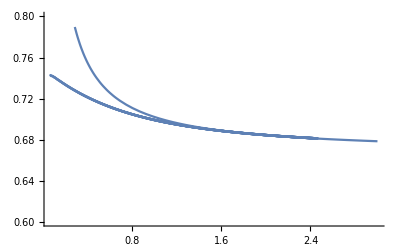

```mathematica
Show[ListPlot[fftab],Plot[2/3+4/9c1/5/x,{x,0.1,3}],PlotRange->{0.6,0.8}]
```